```mathematica
Module[{p,T},
invclausius[p_]:=Solve[p==0.101325*Exp[-5268.134*(1/T-1/373)],T];
Plot[invclausius[p],{p,0.01,1}]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

-Graphics-

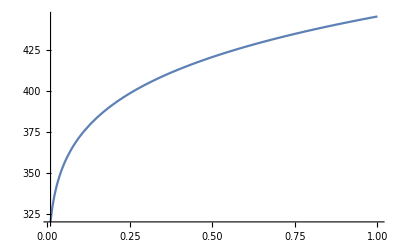

```mathematica
Plot[1/((Log[p/0.101325]/-5268.134)+1/373),{p,0.01,1}]
```